{Binding Energy cs, bs, cc, bc, bb}

{1.056,0.556,0.556,1.056}

{2.2075,2.7075,2.2075,2.7075}

{1.5485,0.5485,1.5485,1.5485}

{2.666,2.666,3.166,3.166}

{3.73,4.73,4.73,4.73}

{Λc 1/2+ 2.287}

{2.26954,4.83976,{3.0782,2.95236,2.47843,2.04279}}

{Σc 1/2+ 2.454}

{2.41127,4.79802,{3.07765,2.95085,2.47595,2.04279}}

{Σc^* 3/2+ 2.518}

{2.51163,4.98638,{3.08004,2.9575,2.48705,2.04279}}

{D 0- 1.867}

{1.83498,3.56425,{3.05587,2.89256,2.39485,2.04279}}

{D^* 1- 2.009}

{2.0086,4.0392,{3.0658,2.9186,2.42789,2.04279}}

{Λb 1/2+ 5.620}

{5.64823,4.59342,{3.07483,2.94307,2.46353,2.04279}}

{Σb 1/2+ 5.813}

{5.83455,4.63391,{3.07541,2.94466,2.46601,2.04279}}

{Σb^* 3/2+ 5.833}

{5.87225,4.72401,{3.07666,2.9481,2.4715,2.04279}}

{B 0- 5.280}

{5.2483,3.12442,{3.04407,2.86276,2.36197,2.04279}}

{B^* 1- 5.325}

{5.32521,3.46003,{3.05334,2.88606,2.38726,2.04279}}

{Ξc 1/2+ 2.469}

{{3.82093,3.32093,3.32093,3.82093},7.2009,{3.09886,3.01146,2.59745,2.04279}}

{Ξc' 1/2+ 2.579}

{{3.92278,3.42278,3.42278,3.92278},7.2009,{3.09886,3.01146,2.59745,2.04279}}

{Ξc^* 3/2+ 2.646}

{{3.98096,3.48096,3.48096,3.98096},7.2009,{3.09886,3.01146,2.59745,2.04279}}

{Ωc 1/2+ 2.695}

{{5.14744,4.14744,4.14744,5.14744},7.2009,{3.09886,3.01146,2.59745,2.04279}}

{Ωc^* 3/2+ 2.766}

{{5.19729,4.19729,4.19729,5.19729},7.2009,{3.09886,3.01146,2.59745,2.04279}}

{Ds 0- 1.968}

{{4.64887,3.64887,3.64887,4.64887},7.2009,{3.09886,3.01146,2.59745,2.04279}}

{Ds^* 1- 2.112}

{{4.71534,3.71534,3.71534,4.71534},7.2009,{3.09886,3.01146,2.59745,2.04279}}

{Ξb 1/2+ 5.794}

{{8.39013,8.89013,8.39013,8.89013},7.2009,{3.09886,3.01146,2.59745,2.04279}}

{Ξb' 1/2+ 5.935}

{{8.51751,9.01751,8.51751,9.01751},7.2009,{3.09886,3.01146,2.59745,2.04279}}

{Ξb^* 3/2+ 5.954}

{{8.53739,9.03739,8.53739,9.03739},7.2009,{3.09886,3.01146,2.59745,2.04279}}

{Ωb 1/2+ 6.046}

{{10.89,11.89,10.89,11.89},7.2009,{3.09886,3.01146,2.59745,2.04279}}

{Ωb^* 3/2+}

{{10.9071,11.9071,10.9071,11.9071},7.2009,{3.09886,3.01146,2.59745,2.04279}}

{Bs 0- 5.367}

{{10.4023,11.4023,10.4023,11.4023},7.2009,{3.09886,3.01146,2.59745,2.04279}}

{Bs^* 1- 5.415}

{{10.4251,11.4251,10.4251,11.4251},7.2009,{3.09886,3.01146,2.59745,2.04279}}

{ηc 0- 2.984}

{{6.90487,4.90487,6.90487,6.90487},7.2009,{3.09886,3.01146,2.59745,2.04279}}

{Jψ 1- 3.097}

{{6.92658,4.92658,6.92658,6.92658},7.2009,{3.09886,3.01146,2.59745,2.04279}}

{ηb 0- 9.399}

{{18.1176,20.1176,20.1176,20.1176},7.2009,{3.09886,3.01146,2.59745,2.04279}}

{Υ 1- 9.460}

{{18.1202,20.1202,20.1202,20.1202},7.2009,{3.09886,3.01146,2.59745,2.04279}}

{Ξcc 1/2+ 3.621}

{{5.61471,4.61471,5.61471,5.61471},7.2009,{3.09886,3.01146,2.59745,2.04279}}

{Ξcc^* 3/2+ 3.714}

{{5.68122,4.68122,5.68122,5.68122},7.2009,{3.09886,3.01146,2.59745,2.04279}}

{My Error}

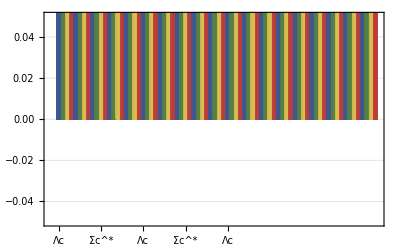

```mathematica
(* run MITBagModel.nb first instead of importing MITBagModel.m *)

m={5.093,1.641,0.279,0,0};
B=0.145^4;
Z=1.83;

{"Binding Energy cs, bs, cc, bc, bb"}
Bcs=-(First[NHadronFitting[{0,1,1,0},-16/3 Cij[2,3],m,B,Z,0]]-2.112)/2
Bbs=-(First[NHadronFitting[{1,0,1,0},-16/3 Cij[1,3],m,B,Z,0]]-5.415)/2
Bcc=-(First[NHadronFitting[{0,2,0,0},-16/3 Cij[2,2],m,B,Z,0]]-3.097)/2
Bbc=-(First[NHadronFitting[{1,1,0,0},-16/3 Cij[1,2],m,B,Z,0]]-6.332)/2
Bbb=-(First[NHadronFitting[{2,0,0,0},-16/3 Cij[1,1],m,B,Z,0]]-9.460)/2

{"Λc 1/2+ 2.287"}
Λc=NHadronFitting[{0,1,0,2},8Cij[4,4],m,B,Z,0]

{"Σc 1/2+ 2.454"}
Σc=NHadronFitting[{0,1,0,2},32/3 Cij[2,4]-8/3 Cij[4,4],m,B,Z,0]

{"Σc^* 3/2+ 2.518"}
ΣcStar=NHadronFitting[{0,1,0,2},-16/3 Cij[2,4]-8/3 Cij[4,4],m,B,Z,0]

{"D 0- 1.867"}
Dq=NHadronFitting[{0,1,0,1},16Cij[2,4],m,B,Z,0]

{"D^* 1- 2.009"}
DqStar=NHadronFitting[{0,1,0,1},-16/3 Cij[2,4],m,B,Z,0]

{"Λb 1/2+ 5.620"}
Λb=NHadronFitting[{1,0,0,2},8Cij[4,4],m,B,Z,0]

{"Σb 1/2+ 5.813"}
Σb=NHadronFitting[{1,0,0,2},32/3 Cij[1,4]-8/3 Cij[4,4],m,B,Z,0]

{"Σb^* 3/2+ 5.833"}
ΣbStar=NHadronFitting[{1,0,0,2},-16/3 Cij[1,4]-8/3 Cij[4,4],m,B,Z,0]

{"B 0- 5.280"}
Bq=NHadronFitting[{1,0,0,1},16Cij[1,4],m,B,Z,0]

{"B^* 1- 5.325"}
BqStar=NHadronFitting[{1,0,0,1},-16/3 Cij[1,4],m,B,Z,0]

{"Ξc 1/2+ 2.469"}
Ξc=NHadronFitting[{0,1,1,1},8Cij[3,4],m,B,Z,Bcs]

{"Ξc' 1/2+ 2.579"}
ΞcPrime=NHadronFitting[{0,1,1,1},16/3 Cij[2,3]+16/3 Cij[2,4]-8/3 Cij[3,4],m,B,Z,Bcs]

{"Ξc^* 3/2+ 2.646"}
ΞcStar=NHadronFitting[{0,1,1,1},-8/3 Cij[2,3]-8/3 Cij[2,4]-8/3 Cij[3,4],m,B,Z,Bcs]

{"Ωc 1/2+ 2.695"}
Ωc=NHadronFitting[{0,1,2,0},32/3 Cij[2,3]-8/3 Cij[3,3],m,B,Z,2Bcs]

{"Ωc^* 3/2+ 2.766"}
ΩcStar=NHadronFitting[{0,1,2,0},-16/3 Cij[2,3]-8/3 Cij[3,3],m,B,Z,2Bcs]

{"Ds 0- 1.968"}
Ds=NHadronFitting[{0,1,1,0},16Cij[2,3],m,B,Z,2Bcs]

{"Ds^* 1- 2.112"}
DsStar=NHadronFitting[{0,1,1,0},-16/3 Cij[2,3],m,B,Z,2Bcs]

{"Ξb 1/2+ 5.794"}
Ξb=NHadronFitting[{1,0,1,1},8Cij[3,4],m,B,Z,Bbs]

{"Ξb' 1/2+ 5.935"}
ΞbPrime=NHadronFitting[{1,0,1,1},16/3 Cij[1,3]+16/3 Cij[1,4]-8/3 Cij[3,4],m,B,Z,Bbs]

{"Ξb^* 3/2+ 5.954"}
ΞbStar=NHadronFitting[{1,0,1,1},-8/3 Cij[1,3]-8/3 Cij[1,4]-8/3 Cij[3,4],m,B,Z,Bbs]

{"Ωb 1/2+ 6.046"}
Ωb=NHadronFitting[{1,0,2,0},32/3 Cij[1,3]-8/3 Cij[3,3],m,B,Z,2Bbs]

{"Ωb^* 3/2+"}
ΩbStar=NHadronFitting[{1,0,2,0},-16/3 Cij[1,3]-8/3 Cij[3,3],m,B,Z,2Bbs]

{"Bs 0- 5.367"}
Bs=NHadronFitting[{1,0,1,0},16Cij[1,3],m,B,Z,2Bbs]

{"Bs^* 1- 5.415"}
BsStar=NHadronFitting[{1,0,1,0},-16/3 Cij[1,3],m,B,Z,2Bbs]

{"ηc 0- 2.984"}
ηc=NHadronFitting[{0,2,0,0},16Cij[2,2],m,B,Z,2Bcc]

{"Jψ 1- 3.097"}
Jψ=NHadronFitting[{0,2,0,0},-16/3 Cij[2,2],m,B,Z,2Bcc]

{"ηb 0- 9.399"}
ηb=NHadronFitting[{2,0,0,0},16Cij[1,1],m,B,Z,2Bbb]

{"Υ 1- 9.460"}
Υ=NHadronFitting[{2,0,0,0},-16/3 Cij[1,1],m,B,Z,2Bbb]

{"Ξcc 1/2+ 3.621"}
Ξcc=NHadronFitting[{0,2,0,1},-8/3 Cij[2,2]+32/3 Cij[2,4],m,B,Z,Bcc]

{"Ξcc^* 3/2+"}
ΞccStar=NHadronFitting[{0,2,0,1},-8/3 Cij[2,2]-16/3 Cij[2,4],m,B,Z,Bcc]

{"My Error"}
BarChart[{(First[Λc]-2.287),
(First[Σc]-2.454),
(First[ΣcStar]-2.518),
(First[Ξc]-2.469),
(First[ΞcPrime]-2.579),
(First[ΞcStar]-2.646),
(First[Ωc]-2.695),
(First[ΩcStar]-2.766),
(First[Dq]-1.867),
(First[DqStar]-2.009),
(First[Ds]-1.968),
(First[DsStar]-2.112),
(First[Λb]-5.620),
(First[Σb]-5.813),
(First[ΣbStar]-5.833),
(First[Ξb]-5.794),
(First[ΞbPrime]-5.935),
(First[ΞbStar]-5.954),
(First[Ωb]-6.046),
(First[Bq]-5.280),
(First[BqStar]-5.325),
(First[Bs]-5.367),
(First[BsStar]-5.415),
(First[ηc]-2.984),
(First[Jψ]-3.097),
(First[ηb]-9.399),
(First[Υ]-9.460),
(First[Ξcc]-3.621)},Frame->True,ChartLabels->{"Λc","Σc","Σc^*","Ξc","Ξc'","Ξc^*","Ωc","Ωc^*","D","D^*","Ds","Ds^*","Λb","Σb","Σb^*","Ξb","Ξb'","Ξb^*","Ωb","B","B^*","Bs","Bs^*","ηc","Jψ","ηb","Υ","Ξcc"},ChartStyle->"DarkRainbow",PlotRange->{-0.05,0.05},GridLines->Automatic,GridLinesStyle->Directive[Gray, Dashed]]
```